```mathematica
ode=y'[x]-Cos[x]==0
```

-Cos[x]+y'[x]==0

```mathematica
generalSolution=FullSimplify[DSolve[ode,y[x],x]]
```

{{y[x]→C[1]+Sin[x]}}

```mathematica
particularSolution=FullSimplify[DSolve[{ode,y[0]==0},y[x],x]]
```

{{y[x]→Sin[x]}}

```mathematica
ya[x_]:=y[x]/.particularSolution[[1]]
```

```mathematica
FullSimplify[D[ya[x],x]]
```

Cos[x]

```mathematica
dyadx[x_]:=Cos[x]
```

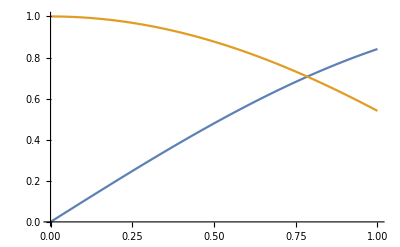

```mathematica
Plot[{ya[x],dyadx[x]},{x,0,1}]
```

```mathematica
Limit[y/(√(1-y^2)),y->1]
```

(-ⅈ) ∞